# The Walking Dead

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
GenerateAccumulatedCoordinates[coordinatesRange_,citiesNumber_]:=Module[{sampledCoordinates,citiesDummy,names,pops,cities},
(*Generate Random Coordinates*)
sampledCoordinates=citiesDummy = Accumulate[RandomReal[{-coordinatesRange,coordinatesRange}, {citiesNumber, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
{sampledCoordinates,names,pops,cities}
]
SyllableToID[a_,labels_]:=Position[labels,a]
ConvertSyllablesToID[sample_,syllablesLabels_]:=Table[SyllableToID[sample[[i]],syllablesLabels],{i,1,Length[sample]}]//Flatten
InTuples[communitiesList_,syllablesLabels_]:=Module[{communitiesIndexes},communitiesIndexes=Map[(Map[Position[syllablesLabels,#]&,#]//Flatten)&,communitiesList];
Tuples[#,2]&/@communitiesIndexes]
ListPlotSong[sample_,syllablesLabels_,OptionsPattern[]]:=Module[{texts,g},texts=Graphics[Text[Style[ToString[#[[1]]],OptionValue[TextSize]],{(sample//Length)+10,#[[2]]},Automatic],AspectRatio->1]&/@({syllablesLabels,Range[syllablesLabels//Length]}//Transpose);
g=ListPlot[
If[OptionValue[Labeling]==True,Labeled[#[[1]],#[[2]]]&,Tooltip[#[[1]],#[[2]]]&]/@({ConvertSyllablesToID[sample,syllablesLabels],ToString/@sample}//Transpose),
ImageSize->OptionValue[ImageSize],
PlotStyle->Directive[Opacity[.75],PointSize[Medium]],
Filling->None,
AxesLabel->{"TimeStep","ID"},
PlotRange->{0,syllablesLabels//Length},
ImagePadding->50,
GridLines->Automatic,
GridLinesStyle->Directive[LightBlue],
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicksStyle->20
];
Show[g,texts,PlotRange->{0,(syllablesLabels//Length)+1}]
]
CalculateInOutRatio[inOutList_]:=(inOutList[[1]]/(inOutList[[1]]+inOutList[[2]]))
ListPlotSongWithCommunities[sample_,communities_,colors_,OptionsPattern[]]:=Module[{frequencyOutput,inOutTotals,labels2,individualCommunitiesInOutRatios,texts,connectionsRules,connectionsWithLabels,rect,rectangles,listPlot,sortedCommunities,wrappers,communitiesIDs,wrappersID},
frequencyOutput=GetTransitionsFrequencies[sample];
inOutTotals=GetCommunitiesInOutTransitionsFrequencies[frequencyOutput,communities,CountLoops->OptionValue[CountLoops]];
labels2=communities//Flatten//DeleteDuplicates;
sortedCommunities=Table[SortBy[i,Position[labels2,#]&],{i,communities}];
wrappers={(#//First)&/@sortedCommunities,(#//Last)&/@sortedCommunities}//Transpose;
communitiesIDs=Table[Position[labels2,#]&/@i//Flatten,{i,sortedCommunities}];
wrappersID={(#//First)&/@communitiesIDs,(#//Last)&/@communitiesIDs}//Transpose;
connectionsRules=wrappersID;
connectionsWithLabels=(UndirectedEdge[labels2[[#[[1]]]],labels2[[#[[2]]]]])&/@connectionsRules;
rect=Rectangle[{0.5,#[[1]]},{(sample//Length)+.5,#[[2]]},RoundingRadius->0]&/@connectionsRules;
rectangles=Graphics[
{
EdgeForm[Directive[Dashing[RandomReal[{0,0}]],Thickness[RandomReal[{.00175,.00175}]],Opacity[.2],colors[[#[[3]]]]]],Opacity[.2],colors[[#[[3]]]],#[[1]]
}
,ImagePadding->500]&/@({rect,Table[i[[1]]/(labels2//Length),{i,wrappersID}],Range[wrappersID//Length]}//Transpose);
individualCommunitiesInOutRatios=CalculateInOutRatio[#]&/@(inOutTotals//Transpose);
texts=Graphics[Text[Style[ToString[PaddedForm[#[[1]],{4,4}]],Bold,OptionValue[TextSize]],{(sample//Length)/2,#[[2]]+.35},Automatic],AspectRatio->1]&/@({individualCommunitiesInOutRatios,connectionsRules[[All,1]]}//Transpose);
listPlot=ListPlotSong[sample,labels2,ImageSize->OptionValue[ImageSize],Labeling->OptionValue[Labeling],TextSize->OptionValue[TextSize]];
Show[{listPlot,rectangles,texts}//Flatten]
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

RandomPointsPlot

RandomPointsMatrix

## Inputs

```mathematica
{vertexSize,vertexLabelSize}={.25,10};
(*Set the number of cities wanted, the x-y coordinates range to sample from, and the number of site types allowd*)
{citiesNumber,coordinatesRange,classesNumber}={4,100,4};
(*Assigns a class type to each point based on a random uniform distribution of probabilities and the number of types defined previously*)
(*Set a vector with the probabilities the walker has to stay in current node or move to the others. This vector is then rotated to generate the "partiteness" mask.*)
movementProbabilitiesVector=ConstantArray[0,classesNumber]//ReplacePart[#,{2->1,3->0}]&;
(*The penalizations matrix is a type-based transitions matrix to be used as mask down the road*)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,classesNumber}];
MatrixForm[penalizationsMatrix]
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0)

## Generate Spatial Setting

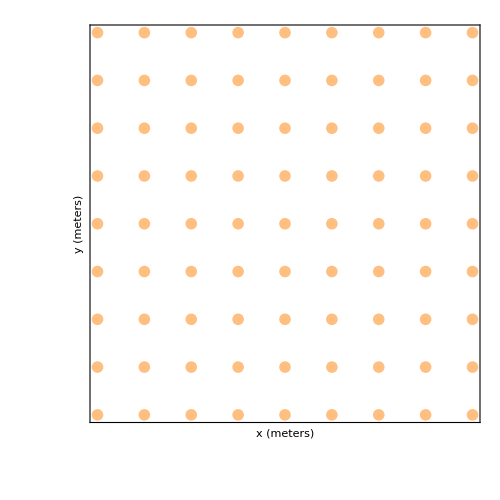

```mathematica
sampledCoordinates=Tuples[Range[-citiesNumber,citiesNumber],2];
distances = CalculateEuclideanDistances[sampledCoordinates];
cities=Transpose[{ToString/@Range[sampledCoordinates//Length],sampledCoordinates,ConstantArray[100,sampledCoordinates//Length]}];
(*Geo-Clustering*)
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
clustersStrings=Table[ToString/@Flatten[Position[cities[[All,2]],#]&/@clusteredCoordinates[[i]]],{i,1,clusteredCoordinates//Length}];
clustersIDs=Position[Map[ToExpression,clustersStrings,Infinity],#][[1,1]]&/@Range[Length[sampledCoordinates]];
(*Plots*)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clustersStrings])]]//Flatten//RandomSample;
ListPlot[clusteredCoordinates,PlotTheme->"RandomPointsPlot",ImageSize->500,PlotStyle->colors]
```

## Analyze

Map

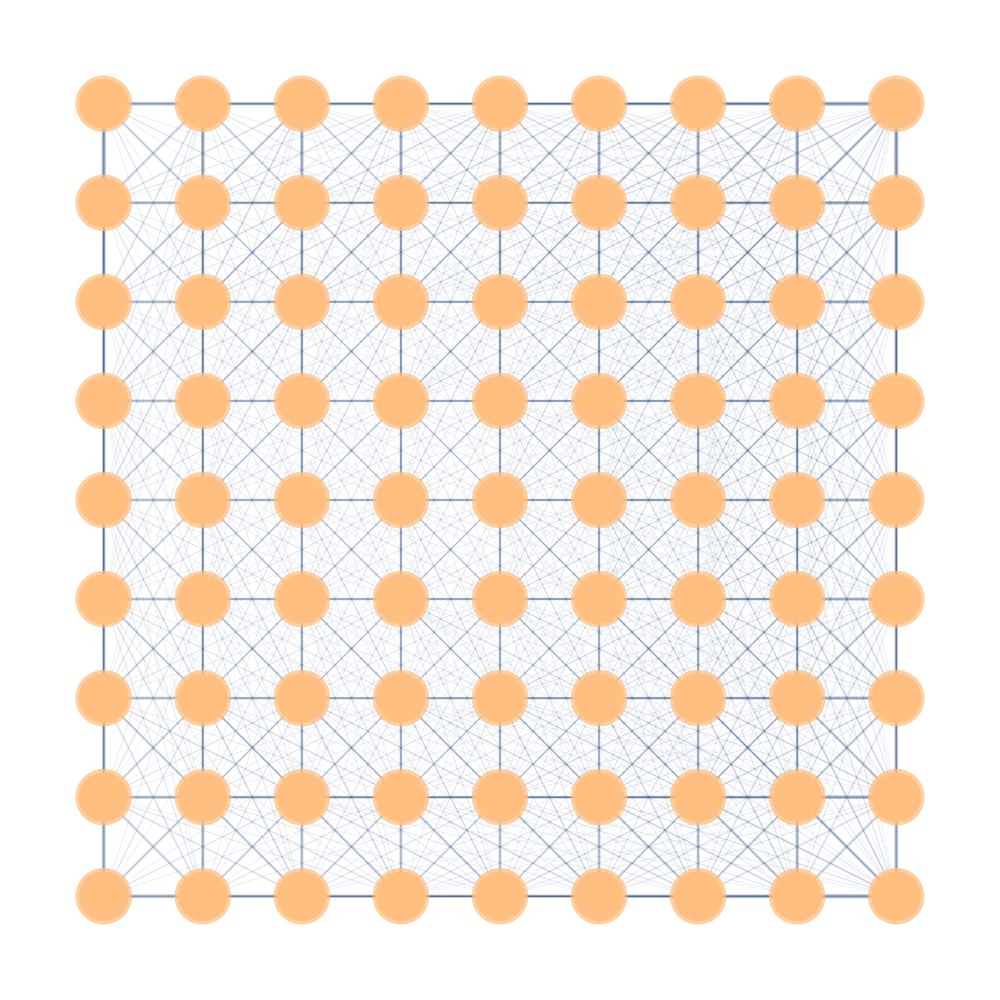

```mathematica
(*This "migration" is replacing the real kernel for the time being. It is based on the inverse of the distance to other nodes.*)
migration = CalculateMigrationProbabilities[distances, .05];
edgeshape2[e_,___]:={Arrowheads[{{.000001,.9}}],Arrow[e]}
stylesSwatch=Directive[Opacity[1],colors[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[clusteredCoordinates//Length];
stylesList=(ToString[#[[1]]]->stylesSwatch[[#[[2]]]])&/@Transpose[{Range[clustersIDs//Length],clustersIDs}];
map = GraphTransitionsFrequenciesWithMax[
  {
Chop[ReplacePart[migration,{i_,i_}->0]//LowerTriangularize,10^-2],
ToString /@ Range[Length[migration]]
   }, .15,
 VertexStyle ->stylesList,
VertexCoordinates ->sampledCoordinates,
VertexSize ->1vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize -> 1000,
LineThickness -> .0075,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both",
ImagePadding->50,
Epilog->Riffle[stylesList[[All,2]],(Disk[#,vertexSize]&/@sampledCoordinates)]
  ]
```

```mathematica
Export["00_clustering.pdf",map,ImageSize->2000,ImageResolution->500]
```

00_clustering.pdf

Mask Movement with Site-Types

```mathematica
(*If the transition between city types is not possible, or improbable, then mask it with the corresponding value. After that, normalize for the probabilities to still add up to one.*)
cityType=RandomChoice[Range[classesNumber],sampledCoordinates//Length]
{cityType[[1]],#}&/@cityType;
```

{3,2,4,2,4,1,1,4,1,1,1,3,3,4,4,4,3,4,3,1,4,1,1,4,2,4,3,4,3,1,2,4,1,3,3,1,1,4,1,4,1,2,2,2,3,3,2,2,3,2,2,2,3,1,2,1,4,1,1,2,4,3,2,3,1,3,4,2,4,4,3,2,4,4,3,3,1,3,4,1,2}

```mathematica
distancesPlot=distances//MatrixPlot[#,ColorFunction->"LakeColors",ImageSize->2000,FrameTicks->None,PlotRangePadding->None,FrameStyle->Directive[Gray,Thick]]&;
penalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
normalizedMaskedMatrix=(#/Total[#])&/@(penalizationsMask*migration);
(*Plots*)
penalizationsMaskPlot=penalizationsMask//MatrixPlot[#,ColorFunction->"LakeColors",ImageSize->2000,FrameTicks->None,PlotRangePadding->None,FrameStyle->Directive[Gray,Thick]]&;
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
normalizedMaskedMatrixPlot=normalizedMaskedMatrix//MatrixPlot[#,ColorFunction->"LakeColors",ImageSize->2000,FrameTicks->None,PlotRangePadding->None,FrameStyle->Directive[Gray,Thick]]&;
```

```mathematica
Grid[{{distancesPlot,penalizationsMaskPlot,normalizedMaskedMatrixPlot}}];
Export["02_Matrices.jpg",%]
```

02_Matrices.jpg

Movement Network

```mathematica
edgeshape2[e_,___]:={Arrowheads[{{.015,.75}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .35,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->.0001*vertexLabelSize,
ImageSize->1000,
LineThickness->.005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both",
ImagePadding->50
  ];
Export["01_Movement.jpg",%,ImageSize->2000,ImageResolution->500]
```

01_Movement.jpg

Markov

```mathematica
kernel=normalizedMaskedMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
MarkovProcessProperties[markov,"LimitTransitionMatrix"]//MatrixPlot[#,ColorFunction->"LakeColors"]&;
```

```mathematica
markov=DiscreteMarkovProcess[initialState,kernel];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
histogram=SmoothHistogram[markovPDF,Frame->True,FrameStyle->Black,PlotStyle->Thickness[.005],ImageSize->1000,Filling->Bottom];
matrix=MatrixPlot[{markovPDF},Frame->False,FrameStyle->Directive[Black,Thick],ColorFunction->ColorData[{"LakeColors","Reverse"}],FrameTicks->{None,All},ImageSize->1000];
violinPDF=DistributionChart[markovPDF,ChartStyle->"LakeColors",AspectRatio->.2,Frame->False,BarOrigin->Left,ImageSize->1000];
PDFandCDF=ListLinePlot[{Accumulate[markovPDF//Sort//Reverse],100*markovPDF//Sort},
Frame->True,
FrameStyle->Thick,
PlotStyle->Thickness[.005],
ImageSize->1000,
PlotLabel->("[Max: "<>ToString[Max[markovPDF]]<>"]::["<>"Mean: "<>ToString[Mean[markovPDF]]<>"]::["<>"Min: "<>ToString[Mean[markovPDF]]<>"]"<>"]::["<>"SD: "<>ToString[StandardDeviation[markovPDF]]<>"]")
];
Grid[{{violinPDF},{matrix},{PDFandCDF}}];
Export["03_MarkovStationary01.pdf",%]
(*MatrixPlot[{tally[[All,2]]},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]*)
```

03_MarkovStationary01.pdf

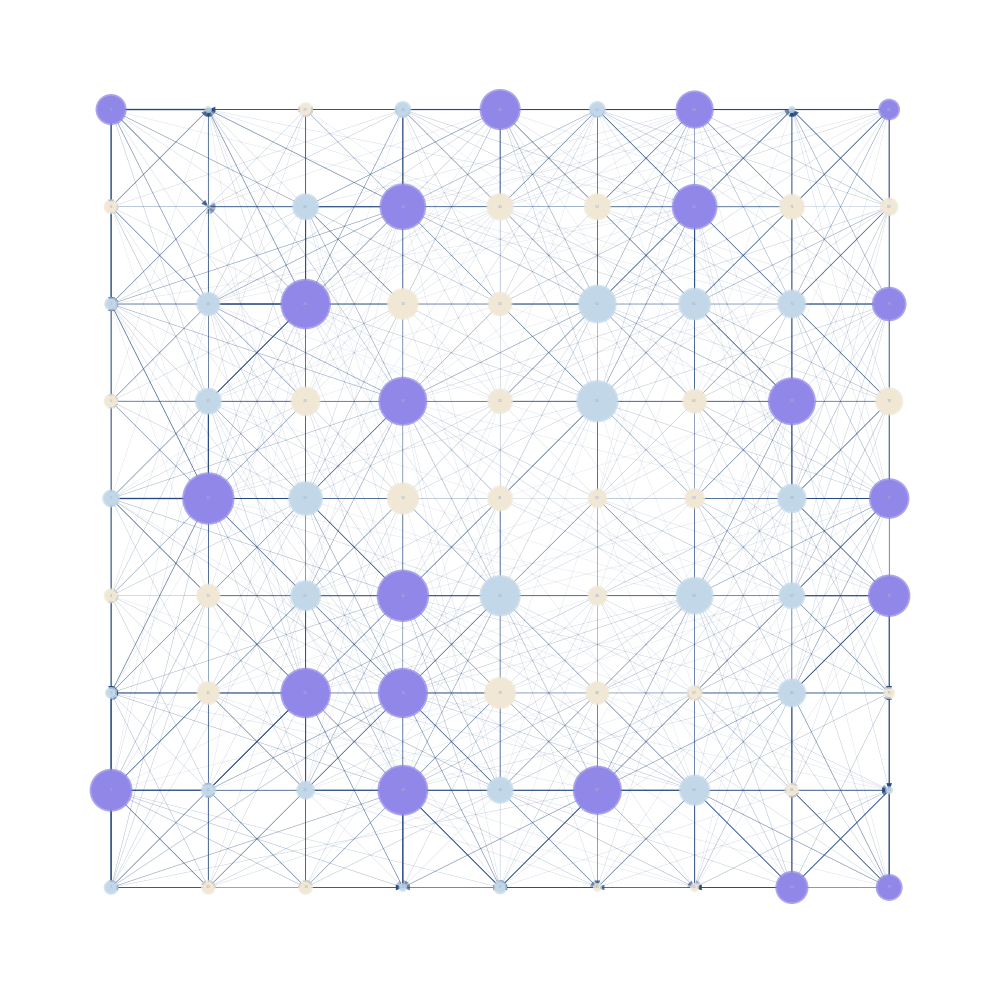

03_MarkovStationary02.jpg

```mathematica
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.0025]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
edgeshape2[e_,___]:={Arrowheads[{{.001,.9}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .1,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize -> Thread[VertexList[graph]->.25*Log[0+7.5*Rescale[markovPDF]]],
VertexLabelStyle->.001,
ImageSize->1000,
LineThickness->.0005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both",
ImagePadding->10
  ]
Export["03_MarkovStationary02.jpg",%,ImageSize->3000,ImageResolution->300]
```

## Targeted Interventions

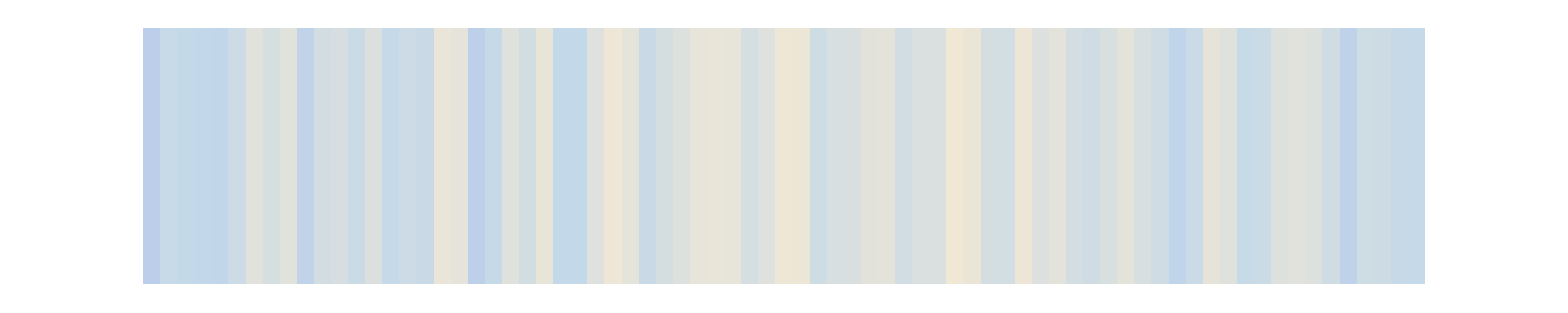

```mathematica
stationaryDistribution=MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]];
MatrixPlot[{stationaryDistribution},ColorFunction->"LakeColors",ImageSize->2000,Frame->None,PlotRangePadding->None]
```

```mathematica
{fractionSprayed,killingEfficacy}={.2,.5};
{fractionRepelled,repellencyEfficacy}={.25,.5};
(**)
{selectionSprayed,selectionRepelled}={Round[fractionSprayed*Length[stationaryDistribution]],Round[fractionRepelled*Length[stationaryDistribution]]};
sortedStationaryDistribution=Sort[stationaryDistribution];
{maxFractionSelection,minFractionSelection}={sortedStationaryDistribution[[1;;selectionSprayed]],Reverse[sortedStationaryDistribution][[1;;selectionRepelled]]};
```

{2,3,4,5,6,1,2,3,4,5,6,1,2,3,4,5,6,1,2,3,4}

{1→77,77→50,50→85,85→84,84→66,66→72,72→39,39→38,38→210,210→78,78→129,129→161,161→189,189→205,205→225,225→200,200→34,34→64,64→77,77→67}

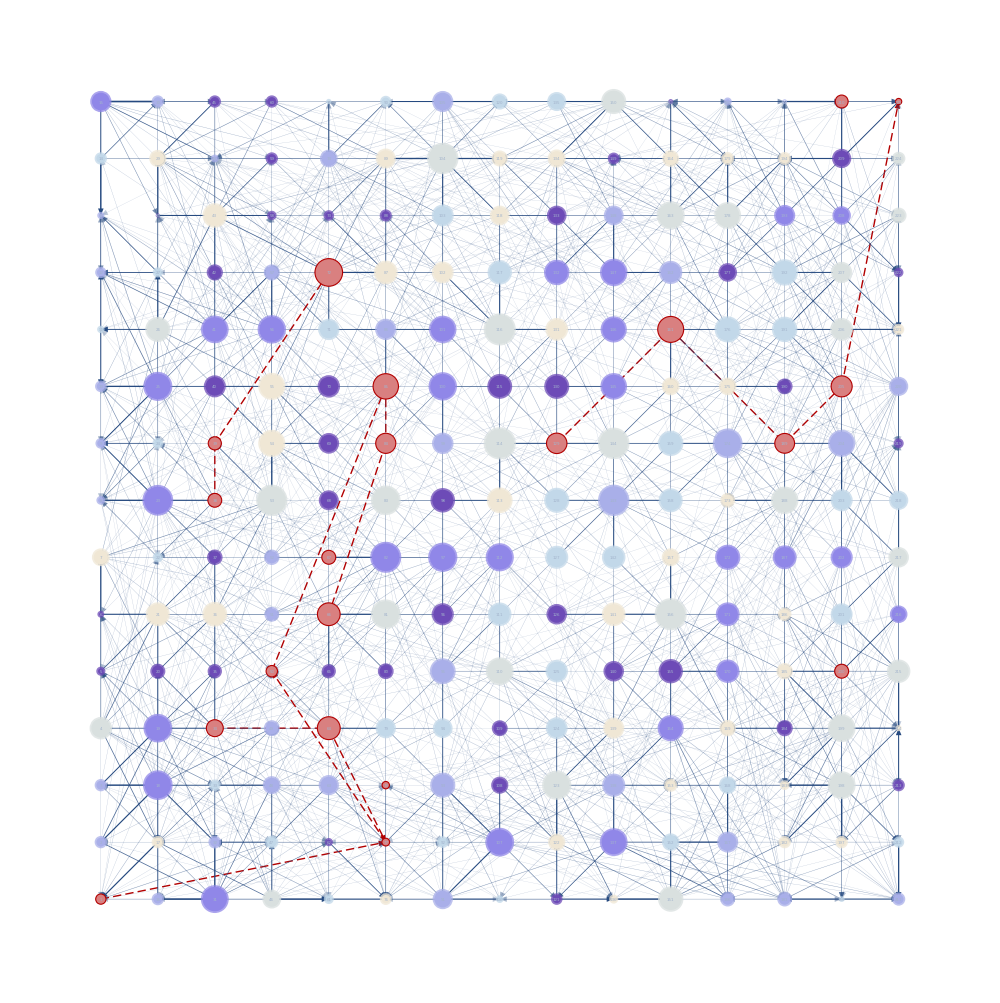

```mathematica
(*BlockRandom[
SeedRandom[123];
sim=RandomFunction[markov,{0,10^4},4*10^3,
Method->{Automatic,"StoppingFunction"->Function[{len,pos},len<1001&&pos≠1||len==1]}
];
]*)
steps=20;
BlockRandom[
SeedRandom[42];
sim=RandomFunction[markov,{0,steps}];
];
path=ToString/@Part[sim["ValueList"],1];
cityType[[#//ToExpression]]&/@path
pathList=(#[[1]]->#[[2]])&/@Subsequences[path,{2}]
HighlightGraph[graph,Flatten[{path[[1;;All]],pathList[[1;;All]]}],GraphHighlightStyle->"Dashed"]
```

```mathematica
(*path=ToString/@Part[sim["ValueList"],1];
pathList=(#[[1]]->#[[2]])&/@Subsequences[path,{2}]
Table[
temp=HighlightGraph[graph,
Flatten[{
path[[1;;i]],
pathList[[1;;(i-1)]]
}]
,GraphHighlightStyle->"Dashed"
];
Export["./images/"<>StringPadLeft[i//ToString,5,"0"]<>".png",temp,ImageResolution->200];
,{i,2,(path//Length)-1}];*)
```